# Core-Shell of type Si/C, Figs. 4h-k & 6f in ‘Manuscript_AS_LBFG_v2-R1.docx’ with AS_LBFG_v2, AS_Calc_v2 June-2023

# 1.1 Un-relaxed atoms 3D

Graphs

```mathematica
SetDirectory["C:\\Users\\Tiberius\\Desktop\\At_Strain_Code0\\AS_Calc_v2\\AS_Calc_v2"];


(*---------------------------------------------------------*)
(*Unrelaxed structure*)
(*Si*)r[1]=Import["fort.38"];
(*C*)r[3]=Import["fort.39"];
(*Si*)r[2]=Import["fort.160"];
(*C*)r[4]=Import["fort.180"];

(*Si*)Nat[1]=Dimensions[r[1]][[1]]
(*C*)Nat[3]=Dimensions[r[3]][[1]]
(*Si*)Nat[2]=Dimensions[r[2]][[1]]
(*C*)Nat[4]=Dimensions[r[4]][[1]]
Nat[1]+Nat[3]+Nat[2]+Nat[4]

x[m_,i_]:=r[m][[i,1]];
y[m_,i_]:=r[m][[i,2]];
z[m_,i_]:=r[m][[i,3]];
(*---------------------------------------------------------*)
```

887

9538

820

9600

20845

```mathematica
(*Unrelaxed structure*)
p1=ListPointPlot3D[{r[1]},PlotStyle->{PointSize[0.009],Blue},PlotRange->All,BoxRatios->{1,1,1}];(*Si*)
p3=ListPointPlot3D[{r[3]},PlotStyle->{PointSize[0.004],Red},PlotRange->All,BoxRatios->{1,1,1}];(*C*)
p2=ListPointPlot3D[{r[2]},PlotStyle->{PointSize[0.009],Blue}];(*Si*)
p4=ListPointPlot3D[{r[4]},PlotStyle->{PointSize[0.004],Red}];(*C*)

Show[p1,p2,PlotRange->All,PlotLabel->"Unrelaxed: Si(blue) ", LabelStyle->Directive[Black,Bold,18],AxesLabel->{"x(A^o)","y(A^o)","z(A^o)"},BoxRatios->{1,1,1}]

Show[p3,p4,PlotRange->All,PlotLabel->"Unrelaxed: C(red)", LabelStyle->Directive[Black,Bold,18],AxesLabel->{"x(A^o)","y(A^o)","z(A^o)"},BoxRatios->{1,1,1},Ticks->{{-40,0,40},{-40,0,40},{0,40,80}}]

Show[p1,p2,p3,p4,PlotRange->All, LabelStyle->Directive[Black,Bold,18],AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

# 1.2 Relaxed atoms 3D; generates - Run 1.1 for Nat1, Nat2, Nat3

```mathematica
SetDirectory["C:\\Users\\Tiberius\\Desktop\\At_Strain_Code0\\AS_Calc_v2\\AS_Calc_v2"];
(*Relaxed structure*)
(*rR[0]=Import["fort.6550"];*)
rR[0]=Import["fort.601"];

Dimensions[rR[0]]

(*Si*)rR[1]=rR[0][[1;;Nat[1]]];
(*C*)rR[3]=rR[0][[Nat[1]+1;;Nat[1]+Nat[3]]];
(*Si*)rR[2]=rR[0][[Nat[1]+Nat[3]+1;;Nat[1]+Nat[3]+Nat[2]]];
(*C*)rR[4]=rR[0][[Nat[1]+Nat[3]+Nat[2]+1;;Nat[1]+Nat[3]+Nat[2]+Nat[4]]];

x[m_,i_]:=rR[m][[i,1]];
y[m_,i_]:=rR[m][[i,2]];
z[m_,i_]:=rR[m][[i,3]];
Dimensions[rR[1]][[1]]-Nat[1]
Dimensions[rR[3]][[1]]-Nat[3]
Dimensions[rR[2]][[1]]-Nat[2]
Dimensions[rR[4]][[1]]-Nat[4]
```

{20845,3}

0

0

0

«1 more identical outputs»

Core-Shell

```mathematica
finNEW[m_,i_]:=If[√(x[m,i]^2+y[m,i]^2+z[m,i]^2)≤RCO,
{x[m,i],y[m,i],z[m,i]},{}];

RCO=19; (*RCO-core radius*)
RCO=30; (*RCO-core radius*)
RCO=18; (*RCO-core radius*)
RCO=20; (*RCO-core radius*)
(*---------------------------------------------------------*)
(*Core-Shell*)
(**)

a1=5.6533 (*GaAs matrix - out*);
a2=6.0583 (*GaSb hemitorus - in*);

a1=3.567(*C matrix - out*);
a2=5.431020511(*Si- in*);

nx=11;
RCS=IntegerPart[RCO+(nx-IntegerPart[RCO/a2])*a1](*core+shell radius*);
epscap=(a2-a1)/a2;
Print["RCS=",RCS]
Print["epscap=",epscap]

(*Placing Ga atoms  in hemitorus+wetting layer*)
(*Gain0R={};
Do[GainR=Append[Gain0R,{finNEW[1,i]}];Gain0R=GainR, {i,1,Nat[-1]}];
GAinR=Partition[Flatten[GainR],3];
Dimensions[GAinR]*)

p1=ListPointPlot3D[{rR[1]},PlotStyle->{PointSize[0.009],Blue},PlotRange->All,BoxRatios->{1,1,1}];
p2=ListPointPlot3D[{rR[2]},PlotStyle->{PointSize[0.009],Blue},PlotRange->All,BoxRatios->{1,1,1}];
p3=ListPointPlot3D[{rR[3]},PlotStyle->{PointSize[0.004],Red}];
p4=ListPointPlot3D[{rR[4]},PlotStyle->{PointSize[0.004],Red}];

Show[p1,p2,PlotLabel->"Ga(blue),Sb(green), Relaxed",BoxRatios->{1,1,1}]
Show[p3,p4,BoxRatios->{1,1,1},PlotRange->All]
Show[p1,p2,p3,p4,BoxRatios->{1,1,1},PlotRange->All]
```

RCS=48

epscap=0.343217

-Graphics3D-

-Graphics3D-

-Graphics3D-

# 1.3 Placing atoms IN and OUT in CS: 2D, yz layer thickness

887

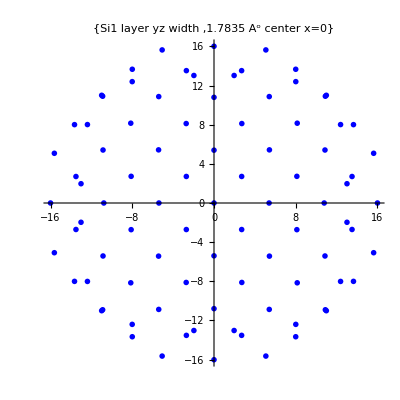

820

-Graphics-

9538

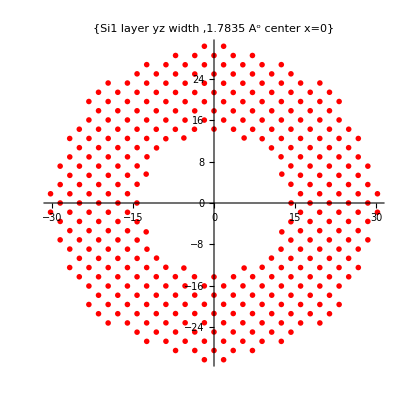

9600

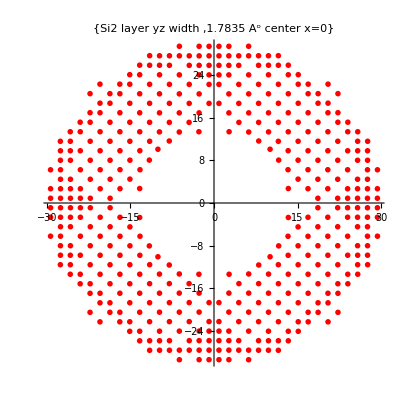

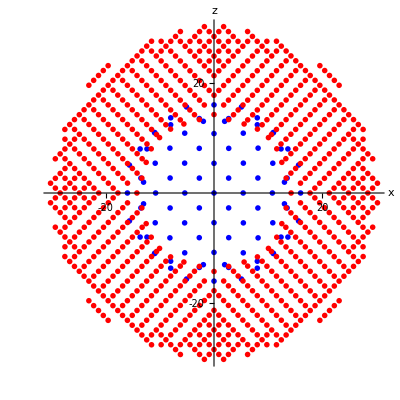

```mathematica
a2=5.431020511; (*Si matrix - in*);
a1=3.567; (*C matrix - out*);
dij1[a_]:=(a √3)/4; (* nearest neighbors*)
dij2[a_]:=a/(√2); (*second nearest neighbors*)
layer=1*a1/2(*10^-4*);(*width of layer*)

(*a1=5.6533 (*GaAs matrix - out*);
a2=6.0584 (*GaSb hemitorus - in*);
layer=4*a1/8(*10^-4*);(*width of layer*)*)

RelCoef=1; (*0 for unrelaxed and any number for relaxed atoms*)
If[RelCoef==0,Si1=r[1];Si2=r[2];C1=r[3];C2=r[4],
Si1=rR[1];Si2=rR[2];C1=rR[3];C2=rR[4]];

dimSi1=Dimensions[Si1][[1]]
Si10={};
Do[
If[
(*Abs[Si1[[i,1]]]≤layer,*)
-1*layer/2≤Si1[[i,1]]≤1*layer/2,
Si11=Append[Si10,Si1[[i;;i,2;;3]]];Si10=Si11,
Si11=Append[Si10, {}];Si10=Si11
], 
{i,1,dimSi1}];
Si111=Partition[Flatten[Si11],2];
w1=ListPlot[Si111,PlotStyle->{PointSize[0.01],Blue},PlotRange->All,PlotLabel->{"Si1 layer yz width ",1*layer"A^o center x=0"},AspectRatio->1/1]
w1=ListPlot[Si111,PlotStyle->{PointSize[0.01],Blue},PlotRange->All,AspectRatio->1/1];

dimSi2=Dimensions[Si2][[1]]
Si20={};
Do[
If[
-1*layer/2≤Si2[[i,1]]≤1*layer/2,
Si21=Append[Si20,Si2[[i;;i,2;;3]]];Si20=Si21,
Si21=Append[Si20, {}];Si20=Si21
], 
{i,1,dimSi2}];
Si211=Partition[Flatten[Si21],2];
w2=ListPlot[Si211,PlotStyle->{PointSize[0.01],Blue},PlotRange->All,PlotLabel->{"Si2 layer yz width ",1*layer"A^o center x=0"},AspectRatio->1/1]
w2=ListPlot[Si211,PlotStyle->{PointSize[0.01],Blue},PlotRange->All,AspectRatio->1/1];

dimC1=Dimensions[C1][[1]]
C10={};
Do[
If[
(*Abs[C1[[i,1]]]≤layer,*)
-1*layer/2≤C1[[i,1]]≤1*layer/2,
C11=Append[C10,C1[[i;;i,2;;3]]];C10=C11,
C11=Append[C10, {}];C10=C11
], 
{i,1,dimC1}];
C111=Partition[Flatten[C11],2];
w3=ListPlot[C111,PlotStyle->{PointSize[0.01],Red},PlotRange->All,PlotLabel->{"Si1 layer yz width ",1*layer"A^o center x=0"},AspectRatio->1/1]
w3=ListPlot[C111,PlotStyle->{PointSize[0.01],Red},PlotRange->All,AspectRatio->1/1];

dimC2=Dimensions[C2][[1]]
C20={};
Do[
If[
-1*layer/2≤C2[[i,1]]≤1*layer/2,
C21=Append[C20,C2[[i;;i,2;;3]]];C20=C21,
C21=Append[C20, {}];C20=C21
], 
{i,1,dimC2}];
C211=Partition[Flatten[C21],2];
w4=ListPlot[C211,PlotStyle->{PointSize[0.01],Red},PlotRange->All,PlotLabel->{"Si2 layer yz width ",1*layer"A^o center x=0"},AspectRatio->1/1]
w4=ListPlot[C211,PlotStyle->{PointSize[0.01],Red},PlotRange->All,AspectRatio->1/1];

Show[w1,w2,w3,w4,PlotRange->All,LabelStyle->Directive[Black,Bold,14],AxesLabel->{Style["x",14,Bold,Black,Italic],Style["z",14,Bold,Black,Italic]},Ticks->{{-30,-20,20,30},{-30,-20,20,30}},AspectRatio->1/1,PlotRange->All];

Show[w1,w2,w3,w4,PlotRange->All,LabelStyle->Directive[Black,Bold,14],AxesLabel->{Style["x",14,Bold,Black,Italic],Style["z",14,Bold,Black,Italic]},Ticks->{{-40,-20,20,40},{-40,-20,20,40}},AspectRatio->1/1,PlotRange->All]

(**)
```

```mathematica
layer
```

1.7835

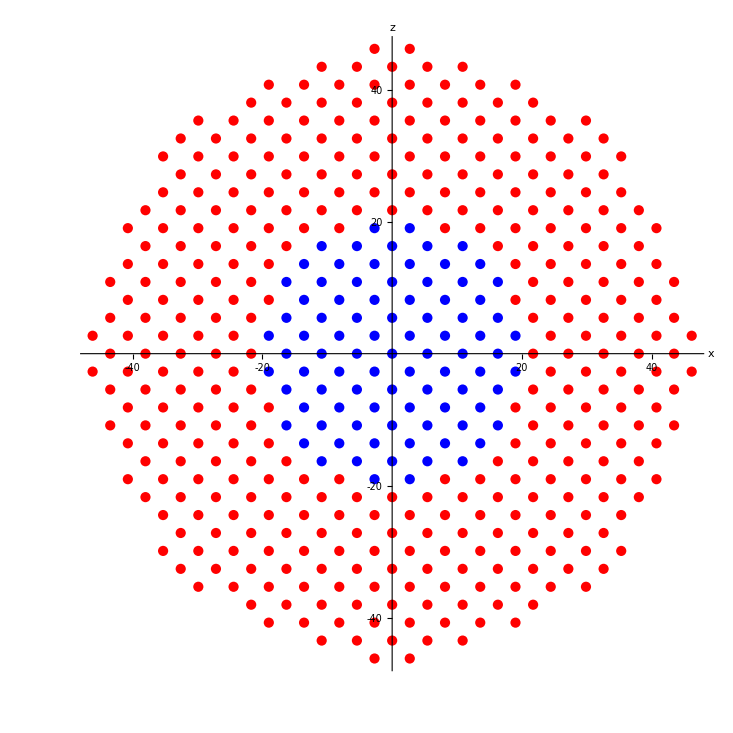
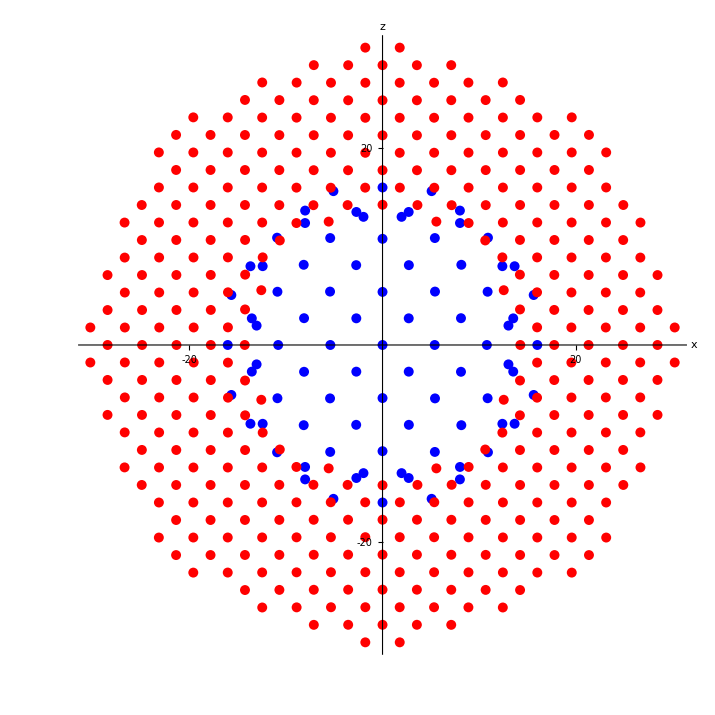
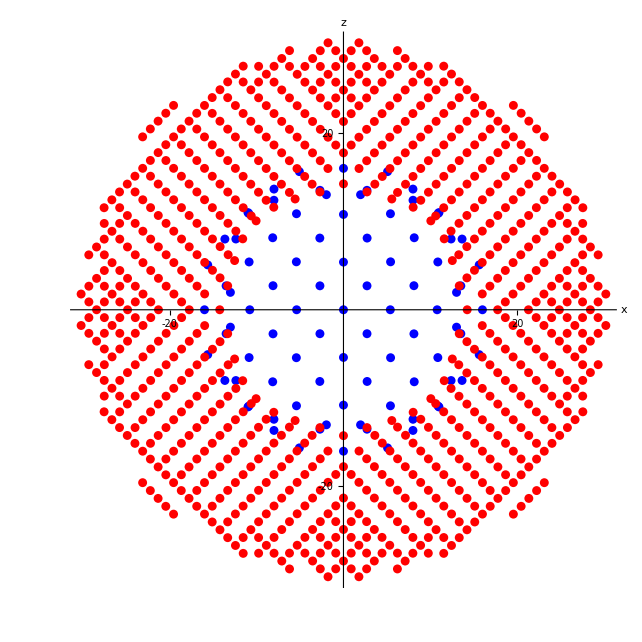
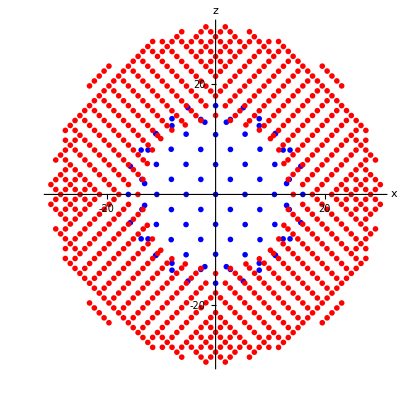
layer=1*a1/4:  unrel:-Graphics- rel: -Graphics-  -Graphics-  -Graphics-

```mathematica
layer
```

1.7835

# 1.4 Strain field calculus

1.4.1 In xy planes results

```mathematica
SetDirectory["C:\\Users\\Tiberius\\Desktop\\At_Strain_Code0\\AS_Calc_v2\\AS_Calc_v2"];

(*z=0 plane*)
(*Ga*)epsxxplane0=Import["fort.1001"] ;(*for xy plane*)
(*Ga*)epsyyplane0=Import["fort.1002"]; (*for xy plane*)
(*Ga*)epszzplane0=Import["fort.1003"]; (*for xy plane*)
(*(*Ga*)epsxyplane0=Import["fort.1004"]; (*for xy plane*)*)
(*Ga*)epshydplane0=Import["fort.1007"]; (*for xy plane*)
epsxxplaneAll0=Import["fort.2011"]; (*for xy plane*)
epsyyplaneAll0=Import["fort.2012"]; (*for xy plane*)
epszzplaneAll0=Import["fort.2013"]; (*for xy plane*)
epshydplaneAll0=Import["fort.2017"]; (*for xy plane*)
(*LPXX0=ListPlot3D[epsxxplane0,PlotStyle->Directive[Opacity[0.3],Blue],PlotLabel->"epsxxplane0", PlotRange->{-0.07,0.03},Mesh->None]*)

LPXX0=ListPlot3D[epsxxplane0,PlotLabel->"epsxxplane0", PlotRange->All]
LPYY0=ListPlot3D[epsyyplane0,PlotLabel->"epsyyplane0", PlotRange->All]
LPZZ0=ListPlot3D[epszzplane0,PlotLabel->"epszzplane0", PlotRange->All]
LPHYD0=ListPlot3D[epshydplane0,PlotLabel->"epshydplane0", PlotRange->All]
(*Show[LPYY0,LPZZ0,LPHYD0, PlotRange->All, Mesh->None]*)
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
(*z=zcord/2 plane*)
(*Ga*)epsxxplane1=Import["fort.1101"]; (*for xy plane*)
(*Ga*)epsyyplane1=Import["fort.1102"]; (*for xy plane*)
(*Ga*)epszzplane1=Import["fort.1103"]; (*for xy plane*)
(*(*Ga*)epsxyplane1=Import["fort.1104"]; (*for xy plane*)*)
(*Ga*)epshydplane1=Import["fort.1107"]; (*for xy plane*)
epsxxplaneAll1=Import["fort.2111"]; (*for xy plane*)
epsyyplaneAll1=Import["fort.2112"]; (*for xy plane*)
epszzplaneAll1=Import["fort.2113"]; (*for xy plane*)
epshydplaneAll1=Import["fort.2117"]; (*for xy plane*)
LPXX1=ListPlot3D[epsxxplane1,PlotLabel->"epsxxplane1", PlotRange->All]
LPYY1=ListPlot3D[epsyyplane1,PlotLabel->"epsyyplane1", PlotRange->All]
LPZZ1=ListPlot3D[epszzplane1,PlotLabel->"epszzplane1", PlotRange->All]
LPHYD1=ListPlot3D[epshydplane1,PlotLabel->"epshydplane1", PlotRange->All]

LPXXAll1=ListPlot3D[epsxxplaneAll1,PlotLabel->"ε_xx",LabelStyle->Directive[Bold,Italic], PlotRange->All];
LPAllYY1=ListPlot3D[epsyyplaneAll1,PlotLabel->"ε_yy",LabelStyle->Directive[Bold,Italic], PlotRange->All];
LPAllZZ1=ListPlot3D[epszzplaneAll1,PlotLabel->"ε_zz",LabelStyle->Directive[Bold,Italic], PlotRange->All];
LPAllHYD1=ListPlot3D[epshydplaneAll1,LabelStyle->Directive[Bold,Italic],PlotLabel->"ε_hyd", PlotRange->All];
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
(*z=zcord/1 plane*)
(*Ga*)epsxxplane2=Import["fort.1201"]; (*for xy plane*)
(*Ga*)epsyyplane2=Import["fort.1202"]; (*for xy plane*)
(*Ga*)epszzplane2=Import["fort.1203"]; (*for xy plane*)
(*(*Ga*)epsxyplane2=Import["fort.1204"]; (*for xy plane*)*)
(*Ga*)epshydplane2=Import["fort.1207"]; (*for xy plane*)

epsxxplaneAll2=Import["fort.2211"];(*for xy plane*)
epsyyplaneAll2=Import["fort.2212"]; (*for xy plane*)
epszzplaneAll2=Import["fort.2213"]; (*for xy plane*)
epshydplaneAll2=Import["fort.2217"]; (*for xy plane*)

LPXX2=ListPlot3D[epsxxplane2,PlotLabel->"epsxxplane2", PlotRange->All]
LPYY2=ListPlot3D[epsyyplane2,PlotLabel->"epsyyplane2", PlotRange->All]
LPZZ2=ListPlot3D[epszzplane2,PlotLabel->"epszzplane2", PlotRange->All]
LPHYD2=ListPlot3D[epshydplane2,PlotLabel->"epshydplane2", PlotRange->All]

LPXXAll2=ListPlot3D[epsxxplaneAll2,PlotLabel->"ε_xx", PlotRange->All];LPYYAll2=ListPlot3D[epsyyplaneAll2,PlotLabel->"ε_yy",LabelStyle->Directive[Bold,Italic], PlotRange->All];
LPZZAll2=ListPlot3D[epszzplaneAll2,PlotLabel->"ε_zz",LabelStyle->Directive[Bold,Italic], PlotRange->All];
LPHYDAll2=ListPlot3D[epshydplaneAll2,LabelStyle->Directive[Bold,Italic],PlotLabel->"ε_hyd", PlotRange->All];
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
(*z=3*zcord/2 plane*)
(*Ga*)epsxxplane3=Import["fort.1301"]; (*for xy plane*)
(*Ga*)epsyyplane3=Import["fort.1302"]; (*for xy plane*)
(*Ga*)epszzplane3=Import["fort.1303"]; (*for xy plane*)
(*(*Ga*)epsxyplane3=Import["fort.1304"]; (*for xy plane*)*)
(*Ga*)epshydplane3=Import["fort.1307"]; (*for xy plane*)
epsxxplaneAll2=Import["fort.2311"]; (*for xy plane*)
epsyyplaneAll2=Import["fort.2312"]; (*for xy plane*)
epszzplaneAll2=Import["fort.2313"]; (*for xy plane*)
epshydplaneAll2=Import["fort.2317"]; (*for xy plane*)
LPXX3=ListPlot3D[epsxxplane3,PlotLabel->"epsxxplane3", PlotRange->All]
LPYY3=ListPlot3D[epsyyplane3,PlotLabel->"epsyyplane3", PlotRange->All]
LPZZ3=ListPlot3D[epszzplane3,PlotLabel->"epszzplane3", PlotRange->All]
LPHYD3=ListPlot3D[epshydplane3,PlotLabel->"epshydplane3", PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

1.4.3 In z direction graphs

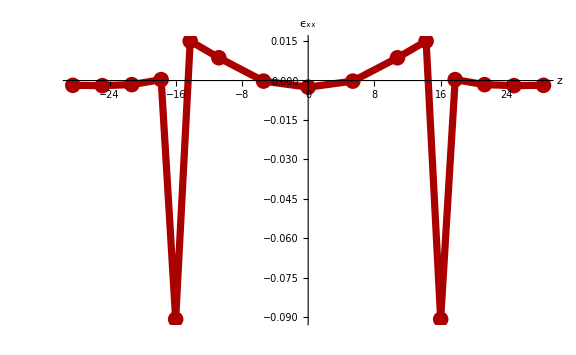

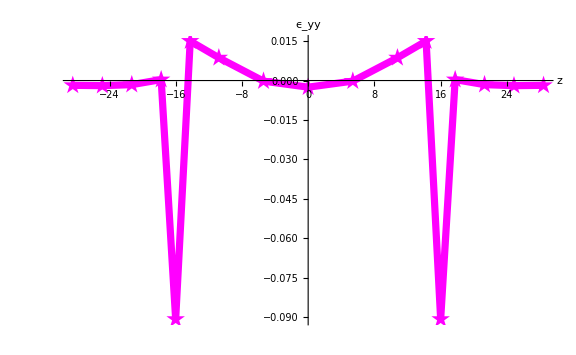

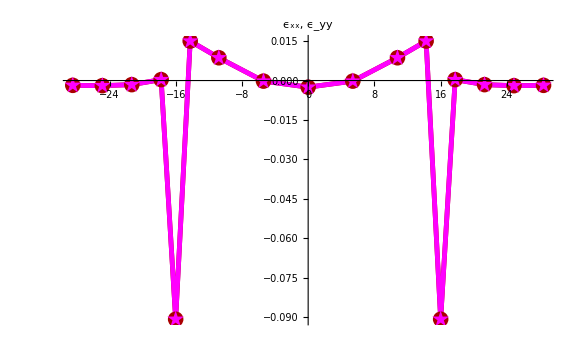

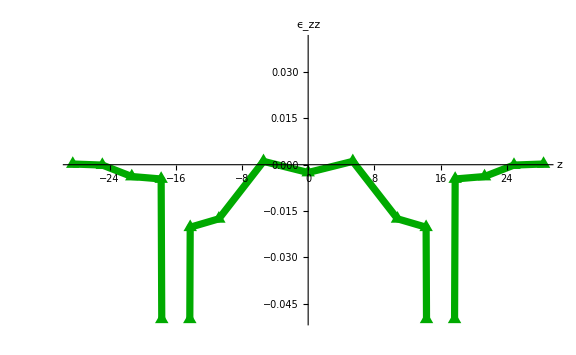

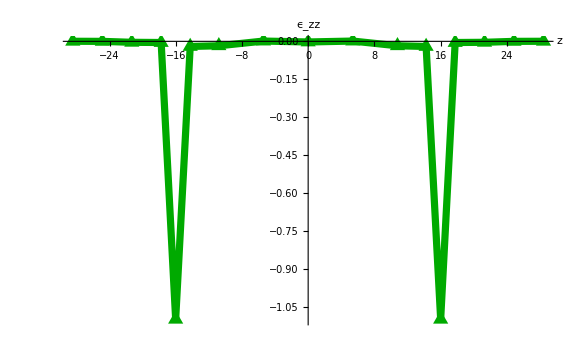

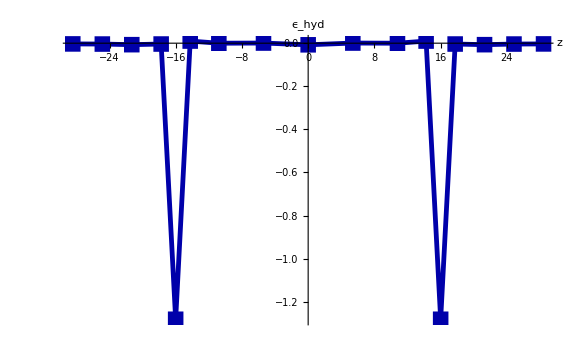

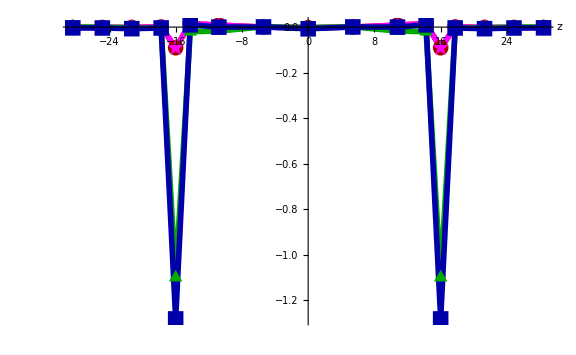

```mathematica
SetDirectory["C:\\Users\\Tiberius\\Desktop\\At_Strain_Code0\\AS_Calc_v2\\AS_Calc_v2"];
epsxx=Sort[Import["fort.3401"],#1[[1]]<#2[[1]]&];
epsyy=Sort[Import["fort.3402"],#1[[1]]<#2[[1]]&];
(**)
 epszz=Sort[Import["fort.3403"],#1[[1]]<#2[[1]]&];
 epshyd=Sort[Import["fort.3404"],#1[[1]]<#2[[1]]&];
 (*
epszz={{-28.4411971559005,0.0002265146055154266},{-24.8695999296746,-0.0001155414530344401},{-21.311446547159,-0.003822822590588915},{-17.76240247224,-0.00461656537299332},(*{-16.00996404726,-1.09934958793434},*){-14.2520098676003,-0.02022620620270349},{-10.7922011298984,-0.01750788147637528},{-5.3957617627106,0.001081781145628291},{-1.527942445821449*^-16,-0.002520326062909528},{5.3957617627106,0.001081781145630067},{10.7922011298984,-0.01750788147637716},{14.2520098676003,-0.02022620620268517},(*{16.00996404726,-1.09934958793434},*){17.76240247224,-0.00461656537299332},{21.311446547159,-0.003822822590607233},{24.8695999296746,-0.0001155414530344401},{28.4411971559006,0.0002265146055900336}};
(**)

(*Ga*)epshyd=Sort[Import["fort.3404"],#1[[1]]<#2[[1]]&];
epshyd={{-28.4411971559005,-0.003423374029330406},{-24.8695999296746,-0.004012276706978846},{-21.311446547159,-0.006935141792849653},{-17.76240247224,-0.003911248458057626},(*{-16.00996404726,-1.28111128325462},*){-14.2520098676003,0.00983065155118662},{-10.7922011298984,-0.0001715958751994373},{-5.3957617627106,0.0006389536214883584},{-1.527942445821449*^-16,-0.007560978188730472},{5.3957617627106,0.0006389536214865821},{10.7922011298984,-0.0001715958752048774},{14.2520098676003,0.009830651551205827},(*{16.00996404726,-1.28111128325462},*){17.76240247224,-0.003911248458057182},{21.311446547159,-0.006935141792885735},{24.8695999296746,-0.004012276706986839},{28.4411971559006,-0.003423374029241588}};
*)
(*;
epsxxAll=Sort[Import["fort.3411"],#1[[1]]<#2[[1]]&];
epsyyAll=Sort[Import["fort.3412"],#1[[1]]<#2[[1]]&]; epszzAll=Sort[Import["fort.3413"],#1[[1]]<#2[[1]]&];epshydAll=Sort[Import["fort.3414"],#1[[1]]<#2[[1]]&];
*)
ListPlot[{epsxx,epsyy,epszz,epshyd},PlotRange->All];

VFFLBFGxx=ListPlot[{epsxx},PlotRange->All,Joined->{True},PlotStyle->{{Darker[Red],Thickness[0.009]}},PlotMarkers->{{●,16}},PlotLabel->Style["ϵ_xx",20,Bold,Black,Italic],AxesLabel->{Style["z",23,Bold,Black,Italic],Style[""]},LabelStyle->Directive[Black,Bold,18],AxesStyle->Thick];
Show[VFFLBFGxx,ImageSize->Large]

VFFLBFGyy=ListPlot[{epsyy},PlotRange->All,Joined->{True},PlotStyle->{{Magenta,Thickness[0.009]}},PlotMarkers->{{★,20}},PlotLabel->Style["ϵ_yy",20,Bold,Black,Italic],AxesLabel->{Style["z",23,Bold,Black,Italic],Style[""]},LabelStyle->Directive[Black,Bold,18],AxesStyle->Thick];
Show[VFFLBFGyy,ImageSize->Large]

VFFLBFGxxyy=ListPlot[{epsxx,epsyy},PlotRange->All(*{{-40,140},All}*),Joined->{True},PlotLabel->Style["ϵ_xx, ϵ_yy",26,Bold,Black,Italic],PlotStyle->{{Darker[Red],Thickness[0.006]},{Magenta,Thickness[0.006]}},PlotMarkers->{{●,16},{★,18}},LabelStyle->Directive[Black,Bold,20],AxesStyle->Thick];
Show[VFFLBFGxxyy,ImageSize->Large]

VFFLBFGzz=ListPlot[{epszz}, PlotRange->{-0.05,0.04},Joined->{True},PlotStyle->{{Darker[Green],Thickness[0.009]}},PlotMarkers->{{▲,16}},PlotLabel->Style["ϵ_zz",20,Bold,Black,Italic],AxesLabel->{Style["z",23,Bold,Black,Italic],Style[""]},LabelStyle->Directive[Black,Bold,18]];
Show[VFFLBFGzz,ImageSize->Large]

VFFLBFGzz1=ListPlot[{epszz},PlotRange->All, Joined->{True},PlotStyle->{{Darker[Green],Thickness[0.009]}},PlotMarkers->{{▲,18}},PlotLabel->Style["ϵ_zz",26,Bold,Black,Italic],AxesLabel->{Style["z",23,Bold,Black,Italic],Style[""]},LabelStyle->Directive[Black,Bold,20]];
Show[VFFLBFGzz1,ImageSize->Large]

VFFLBFGhyd=ListPlot[{epshyd},PlotRange->All, Joined->{True},PlotStyle->{{Darker[Blue],Thickness[0.006]}},PlotMarkers->{{■,16}},PlotLabel->Style["ϵ_hyd",20,Bold,Black,Italic],AxesLabel->{Style["z",23,Bold,Black,Italic],Style[""]},LabelStyle->Directive[Black,Bold,18]];
Show[VFFLBFGhyd,ImageSize->Large]

VFFLBFG=ListPlot[{epsxx,epsyy,epszz,epshyd},PlotRange->All,Joined->{True},PlotStyle->{{Darker[Red],Thickness[0.007]},{Magenta,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Darker[Blue],Thickness[0.007]}},PlotMarkers->{{●,16},{★,18},{▲,16},{■,16}},PlotLabel->Style["",20,Bold,Black,Italic],AxesLabel->{Style["z",23,Bold,Black,Italic],Style[""]},LabelStyle->Directive[Black,Bold,18],AxesStyle->Thick];
Show[VFFLBFG,ImageSize->Large]
```

# 1.5 Misfit dislocations

```mathematica
SetDirectory["C:\\Users\\Tiberius\\Desktop\\At_Strain_Code0\\AS_Calc_v2\\AS_Calc_v2"];
Clear[MDSi1]
(*Si1!!!*)(*mdSi1=Import["temp1571.dat"];*)
mdSi1=Import["fort.571"];
dimSi1=Dimensions[mdSi1][[1]]

mdSi10={};
Do[
If[0≤mdSi1[[i,3]]≤100&&Abs[mdSi1[[i,1]]]≤100&&0<mdSi1[[i,2]]≤100,MDSi1=Append[mdSi10,mdSi1[[i]]];
(*If[-0≤mdSi1[[i,3]]≤40&&0<mdSi1[[i,1]]≤70&&0<mdSi1[[i,2]]≤70,MDSi1=Append[mdSi10,mdSi1[[i]]];*)
mdSi10=MDSi1],
 {i,1,dimSi1}];
MDSi1[[1,3]];
MDSi1;
Dimensions[MDSi1][[1]]
Si1List=ListPointPlot3D[MDSi1,PlotStyle->Directive[Blue,PointSize[0.008]],PlotRange->All]
```

1640

412

-Graphics3D-

```mathematica
Clear[MDSi2]
(*Ga!!!*)(*mdSi2=Import["temp1572.dat"];*)
mdSi2=Import["fort.572"];
dimSi2=Dimensions[mdSi2][[1]]

mdSi20={};
Do[
If[0≤mdSi2[[i,3]]≤100&&Abs[mdSi2[[i,1]]]≤100&&0<mdSi2[[i,2]]≤100,MDSi2=Append[mdSi20,mdSi2[[i]]];(*If[0≤mdSi2[[i,3]]≤40&&0<mdSi2[[i,1]]≤200&&0<mdSi2[[i,2]]≤70,MDSi2=Append[mdSi20,mdSi2[[i]]];*)mdSi20=MDSi2],
 {i,1,dimSi2}];
MDSi2[[1,3]];
MDSi2;
Si2List=ListPointPlot3D[MDSi2,PlotStyle->Directive[Darker[Blue],PointSize[0.008]],PlotRange->All]
```

1372

-Graphics3D-

```mathematica
Clear[MDC1]
(*Ga!!!*)(*mdC1=Import["temp1573.dat"];*)
mdC1=Import["fort.573"];
dimC1=Dimensions[mdC1][[1]]

mdC10={};
Do[
If[0≤mdC1[[i,3]]≤100&&Abs[mdC1[[i,1]]]≤100&&0<mdC1[[i,2]]≤100,MDC1=Append[mdC10,mdC1[[i]]];(*If[0≤mdC1[[i,3]]≤40&&0<mdC1[[i,1]]≤200&&0<mdC1[[i,2]]≤200,MDC1=Append[mdC10,mdC1[[i]]];*)mdC10=MDC1],
 {i,1,dimC1}];
MDC1[[1,3]];
MDC1;
C1List=ListPointPlot3D[MDC1,PlotStyle->Directive[Red,PointSize[0.008]],PlotRange->All]
```

2160

-Graphics3D-

```mathematica
Clear[MDC2]
(*Ga!!!*)(*mdC2=Import["temp1574.dat"];*)
mdC2=Import["fort.574"];
dimC2=Dimensions[mdC2][[1]]

mdC20={};
Do[
If[0≤mdC2[[i,3]]≤100&&Abs[mdC2[[i,1]]]≤200&&0<mdC2[[i,2]]≤200,MDC2=Append[mdC20,mdC2[[i]]];(*If[0≤mdC2[[i,3]]≤40&&0<mdC2[[i,1]]≤200&&0<mdC2[[i,2]]≤200,MDC2=Append[mdC20,mdC2[[i]]];*)mdC20=MDC2],
 {i,1,dimC2}];
MDC2[[1,3]];
MDC2;
C2List=ListPointPlot3D[MDC2,PlotStyle->Directive[Red,PointSize[0.008]],BoxRatios->{1/1,1/2,1/2},PlotRange->All]
```

2348

-Graphics3D-

```mathematica
(*PlotLabel->{"relaxed"},*)
Show[Si1List,Si2List,C1List,C2List,PlotRange->All,LabelStyle->Directive[Black,Bold,20],AxesLabel->{x,y,z},BoxRatios->{1/1,1/2,1/2},Ticks->{{-20,0,20},{0,20},{0,20}},TicksStyle->Directive[14]];
Show[%,ImageSize->Large]
```

-Graphics3D-

# 1.6 Figs 4h-k

CS20SiC_CSQD1 - 13 Figs. 4h, 4i, 4j, 4k 
misfit=0.035

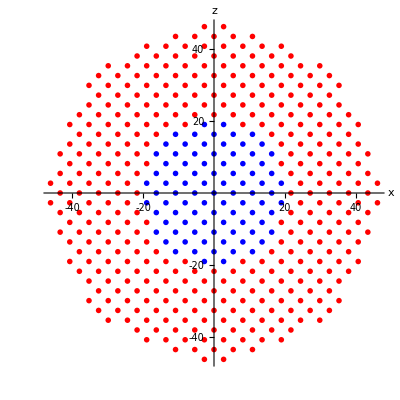
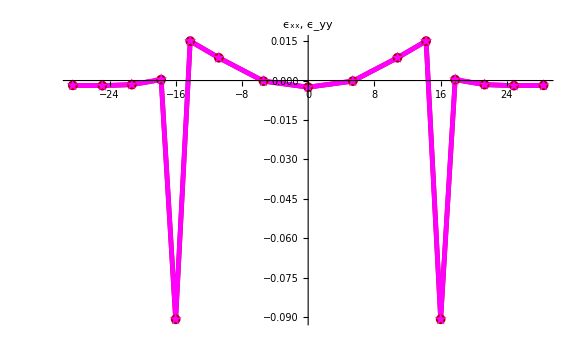
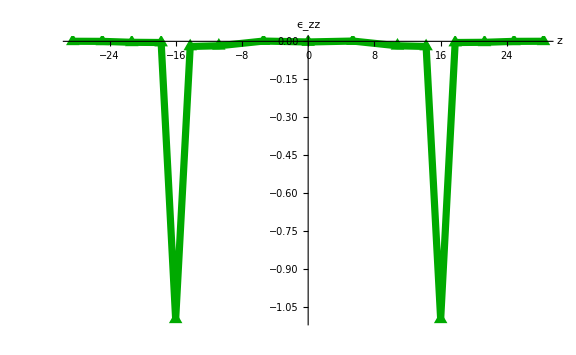
layer=4*a1/8:-Graphics-unrel: rel: -Graphics-


-Graphics- -Graphics- -Graphics- -Graphics-
 -Graphics- -Graphics- -Graphics-

misfit=0.035
 -Graphics3D-

CS19SiC_CSQD1-13 Figs. 4h, 4i, 4j, 4k

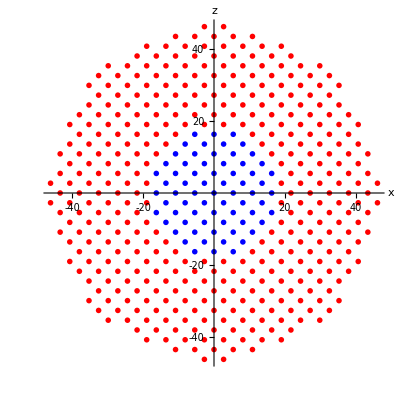
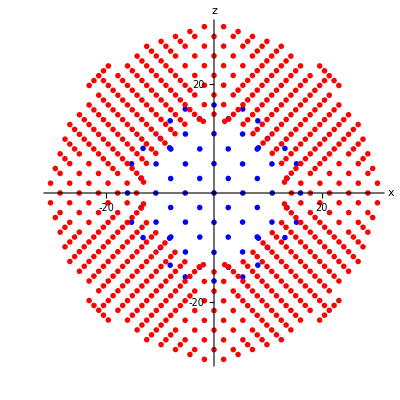
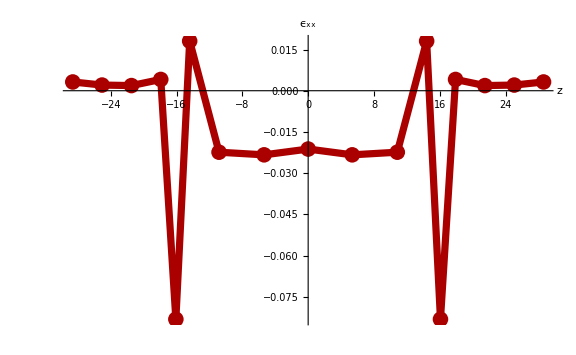
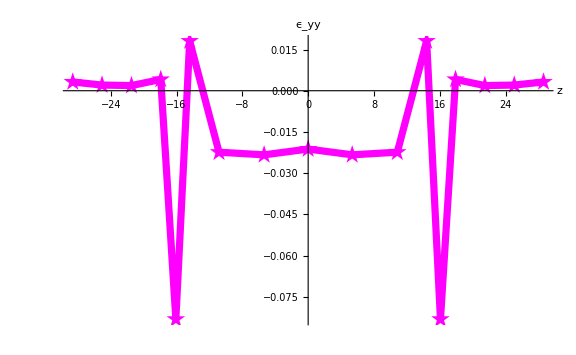
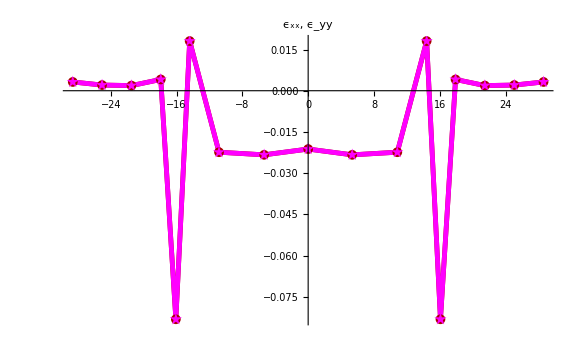
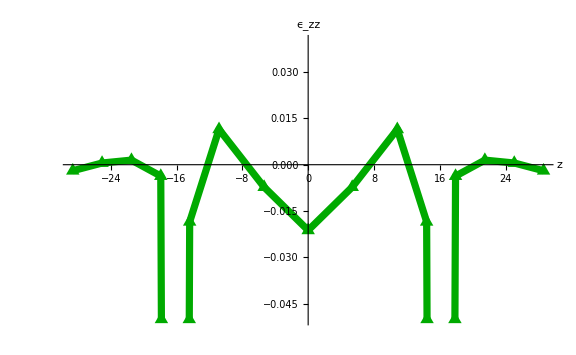
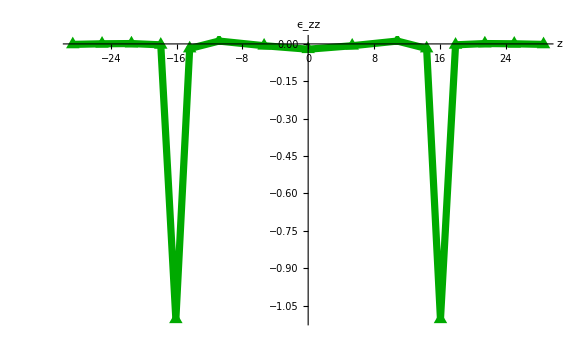
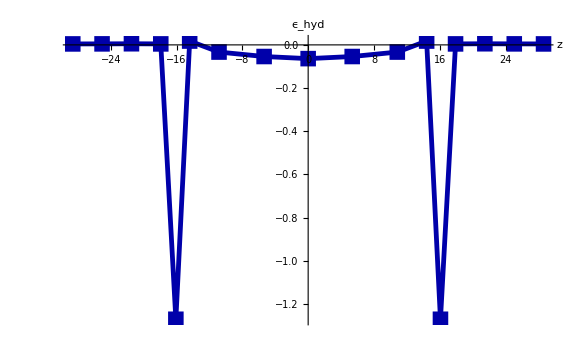
a1=3.567(*C matrix - out*); a2=5.431020511(*Si- in*);
layer thickness = a1/2.
layer=4*a1/8:-Graphics-unrel: rel: -Graphics-
-Graphics-  -Graphics-  -Graphics- -Graphics- -Graphics-  -Graphics-  -Graphics-

-Graphics3D-